## Calculating An Example for the Crossing Case. Using spt1 (x) = -x+5/4, spt2(x) = x+1/4, s0 = 1. Therefore two crossing points x1 = 1/4, x3 = 3/4. And we introduce x2 = 1/2 to divide the domain. Made by Hansen Pei. 12/11/2019

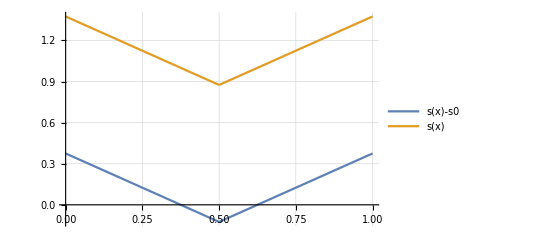

```mathematica
(*Initialization*)
F = 1;
spt1[x_]:=-x+5/4 + 1/8
spt2[x_]:= x+1/4 + 1/8
x1 = 3/8;x2=1/2;x3=5/8;
s[x_]:=Piecewise[{
{spt1[x],0<=x≤x2},
{spt2[x],x2<x≤1}}]
s0 = 1;
Plot[{s[x]-s0,s[x]},{x,0,1},GridLines->Automatic,PlotLegends->"Expressions"]
```

# Interval 1 [0, 3/8)

```mathematica
(*Integrand in mu1[x]*)
Refine[Integrate[(2*F*s0)/(s[xv]^2-s0^2),{xv,0,x},Assumptions->x∈Reals],{0<x<x1}]
```

Log[(57-24 x)/(57-152 x)]

```mathematica
(*Defn of mu1[x]*)
mu1[x_]=Exp[Log[(57-24 x)/(57-152 x)]]//Simplify
```

(57-24 x)/(57-152 x)

```mathematica
(*Integrand in xi1[x]*)
Refine[Integrate[(s[xv]*mu1[xv])/(s[xv]^2-s0^2),{xv,0,x},Assumptions->x∈Reals],{0<x<x1}]//Simplify
```

(8 x (-8+Log[27])-3 Log[27]+(9-24 x) Log[3-8 x])/(19 (-3+8 x))

```mathematica
I1[x_]:=(8 x (-8+Log[27])-3 Log[27]+(9-24 x) Log[3-8 x])/(19 (-3+8 x))
```

```mathematica
(*Defn of xi1[x]*)
xi1[x_]= (-2F*c)/mu1[x]*((8 x (-8+Log[27])-3 Log[27]+(9-24 x) Log[3-8 x])/(19 (-3+8 x))) + a1/mu1[x] //Simplify
```

(19 a1 (-3+8 x)-16 c x (-8+Log[27])+6 c Log[27]+6 c (-3+8 x) Log[3-8 x])/(-57+24 x)

# Interval 2 [3/8, 1/2)

```mathematica
(*Integrand in mu2[x]*)
Refine[Integrate[(-2*F*s0)/(s[xv]^2-s0^2),{xv,x,x2},Assumptions->x∈Reals],{x1<x<x2}]
```

-Log[-15+240/(19-8 x)]

```mathematica
(*Defn of mu2[x]*)
mu2[x_]=Exp[-Log[-15+240/(19-8 x)]]//Simplify
```

(19-8 x)/(15 (-3+8 x))

```mathematica
(*Integrand in xi2[x]*)
Refine[Integrate[(s[xv]*mu2[xv])/(s[xv]^2-s0^2),{xv,x,x2}],{x1<x<x2}]//Simplify
```

Integrate::pwrl: Unable to prove that integration limits {1/2,x} are real. Adding assumptions may help.

(-32+64 x+(3-8 x) Log[-3+8 x])/(15 (-3+8 x))

```mathematica
I2[x_]:=(-32+64 x+(3-8 x) Log[-3+8 x])/(15 (-3+8 x))
```

```mathematica
(*Defn of xi2[x]*)
xi2[x_]= (2F*c)/mu2[x]*((-32+64 x+(3-8 x) Log[-3+8 x])/(15 (-3+8 x))) + a2/mu2[x] //Simplify
```

(64 c (1-2 x)-15 a2 (-3+8 x)+2 c (-3+8 x) Log[-3+8 x])/(-19+8 x)

# Interval 3 [1/2, 5/8)

```mathematica
(*Integrand in mu3[x]*)
Refine[Integrate[(2*F*s0)/(s[xv]^2-s0^2),{xv,x2,x},Assumptions->x∈Reals],{x2<x<x3}]
```

Log[(75-120 x)/(11+8 x)]

```mathematica
(*Defn of mu3[x]*)
mu3[x_]=Exp[Log[(75-120 x)/(11+8 x)]]//Simplify
```

(75-120 x)/(11+8 x)

```mathematica
(*Integrand in xi3[x]*)
Refine[Integrate[(s[xv]*mu3[xv])/(s[xv]^2-s0^2),{xv,x2,x},Assumptions->x∈Reals],{x2<x<x3}]//Simplify
```

(-32+64 x-15 (11+8 x) Log[1/15 (11+8 x)])/(11+8 x)

```mathematica
I3[x_]:=(-32+64 x-15 (11+8 x) Log[1/15 (11+8 x)])/(11+8 x)
```

```mathematica
(*Defn of xi3[x]*)
xi3[x_]= (-2F*c)/mu3[x]*((-32+64 x-15 (11+8 x) Log[1/15 (11+8 x)])/(11+8 x)) + a3/mu3[x] //Simplify
```

-(64 c (1-2 x)+a3 (11+8 x)+30 c (11+8 x) Log[1/15 (11+8 x)])/(15 (-5+8 x))

# Interval 4 [5/8, 1]

```mathematica
(*Integrand in mu4[x]*)
Refine[Integrate[(-2*F*s0)/(s[xv]^2-s0^2),{xv,x,1},Assumptions->x∈Reals],{x3<x<1}]
```

-Log[(3 (11+8 x))/(19 (-5+8 x))]

```mathematica
itg = -Log[(3 (11+8 x))/(19 (-5+8 x))]//Simplify
```

-Log[(3 (11+8 x))/(19 (-5+8 x))]

```mathematica
(*Defn of mu4[x]*)
mu4[x_]=Exp[-Log[(3 (11+8 x))/(19 (-5+8 x))]]//Simplify
```

(19 (-5+8 x))/(33+24 x)

```mathematica
(*Integrand in xi4[x]*)
Refine[Integrate[(s[xv]*mu4[xv])/(s[xv]^2-s0^2),{xv,x,1},Assumptions->x∈Reals],{x3<x<1}]//Simplify
```

(64 (-1+x)+19 (11+8 x) Log[19/(11+8 x)])/(33+24 x)

```mathematica
I4[x_]:=(64 (-1+x)+19 (11+8 x) Log[19/(11+8 x)])/(33+24 x)
```

```mathematica
(*Defn of xi4[x]*)
xi4[x_]= (2F*c)/mu4[x]*((64 (-1+x)+19 (11+8 x) Log[19/(11+8 x)])/(33+24 x)) + a4/mu4[x] //Simplify
```

(128 c (-1+x)+3 a4 (11+8 x)+38 c (11+8 x) Log[19/(11+8 x)])/(19 (-5+8 x))

## Now we use continuity of xi[x] at each joint:

```mathematica
Limit[xi1[x],x->0]//Simplify
Limit[xi1[x],x->x1]
Limit[xi2[x],x->x1]
Limit[xi2[x],x->x2]//Simplify
Limit[xi3[x],x->x2]//Simplify
Limit[xi3[x],x->x3,Direction->"FromBelow"]
Limit[xi4[x],x->x3,Direction->"FromAbove"]
Limit[xi4[x],x->1]
```

a1

-c

-c

a2

a3

DirectedInfinity[2 a3-2 c (1-120 Log[2]+30 Log[3]+30 Log[5])]

DirectedInfinity[6 a4-6 c+76 c Log[19/16]]

a4

# Normalizing for Σ(x)

```mathematica
limI1 = Limit[I1[x],x->x1,Direction->"FromBelow"]//Simplify
limI2 = Limit[I2[x],x->x1,Direction->"FromAbove"]//Simplify
limI3 = Limit[I3[x],x->x3,Direction->"FromBelow"]//Simplify
limI4 = Limit[I4[x],x->x3,Direction->"FromAbove"]
```

∞

-∞

1/2-15 Log[16/15]

1/48 (-24+304 Log[19/16])

-0.468078

0.588385

```mathematica
SigmaDEta1[x_]:=((2*s[x]/mu1[x])*(-I1[x]-limI4)+1)/(s[x]^2-1)
SigmaDEta2[x_]:=((2*s[x]/mu2[x])*(I2[x]+limI3)+1)/(s[x]^2-1)
SigmaDEta3[x_]:=((2*s[x]/mu3[x])*(-I3[x]+limI3)+1)/(s[x]^2-1)
SigmaDEta4[x_]:=((2*s[x]/mu4[x])*(I4[x]-limI4)+1)/(s[x]^2-1)
```

## Plot of Σ(x)/η = f(x), int[f] = 1/eta, eta = 1/int

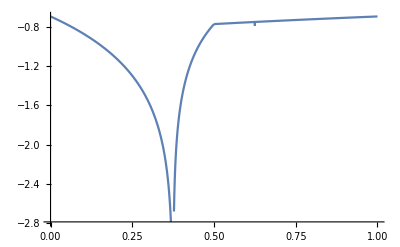

```mathematica
p1 =Plot[SigmaDEta1[x],{x,0,x1}];
p2 = Plot[SigmaDEta2[x],{x,x1,x2}];
p3 = Plot[SigmaDEta3[x],{x,x2,x3}];
p4 = Plot[SigmaDEta4[x],{x,x3,1}];
Show[p1,p2,p3,p4,PlotRange->All]
```

## η = 1/∫[Σ(x)/η]ⅆx

```mathematica
SigmaDEtaTotal = NIntegrate[SigmaDEta1[x],{x,0,x1}]+NIntegrate[SigmaDEta2[x],{x,x1,x2}]+
NIntegrate[SigmaDEta3[x],{x,x2,x3}]+ NIntegrate[SigmaDEta4[x],{x,x3,1}]
```

-0.985102

```mathematica
1/SigmaDEtaTotal//InputForm(*Value of eta*)
```

-1.015123552349955

```mathematica
c=-1.015123552349955;
a1 = a4;
a2 = a3;
a3 = 2* limI3*c;
a4 = -2*limI4*c
```

1.19457

# Save Data

```mathematica
xi[x_]:=Piecewise[{
{xi1[x],0<=x<=x1},
{xi2[x],x1<x≤x2},
{xi3[x],x2<x≤x3},
{xi4[x],x3<x≤1}}]
```

```mathematica
xdata = Subdivide[0,1,2001]//N;
sdata = s /@ xdata//N;
xidata = xi/@ xdata//N;
etadata = Table[-1.015123552349955,2002];
```

```mathematica
datavert = Flatten/@Transpose[{xdata,xidata,sdata, etadata}];
```

```mathematica
Export["D:\\Research with Dr Rossi\\Mathematica Scratch\\analytical_w_crossing_logplus18.csv", datavert, TableHeadings-> {"xdata","xidata","sdata", "etadata"}]
```

D:\Research with Dr Rossi\Mathematica Scratch\analytical_w_crossing_logplus18.csv